# Notebook for : Inhomogeneous Cosmology - Gravitational Radiation In Bianchi Backgrounds by Adams et al

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
January 29, 2021

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book And Review Article

```mathematica
Hyperlink["Inhomogeneous Cosmology - Gravitational Radiation In Bianchi Backgrounds by Adams et al",
"http://adsabs.harvard.edu/pdf/1982ApJ...253....1A"]
```

[Inhomogeneous Cosmology - Gravitational Radiation In Bianchi Backgrounds by Adams et al](http://adsabs.harvard.edu/pdf/1982ApJ...253....1A)

```mathematica
Hyperlink["Mathematica For Physicists Book By Zimmerman",
"https://library.wolfram.com/infocenter/Books/4539/"]
```

[Mathematica For Physicists Book By Zimmerman](https://library.wolfram.com/infocenter/Books/4539/)

```mathematica
Hyperlink["Zimmerman Homepage",
"https://pages.uoregon.edu/rlz/"]
```

[Zimmerman Homepage](https://pages.uoregon.edu/rlz/)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 29 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Line Element and Metric

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 1

```mathematica
Clear[eq1]
eq1 = 
 Exp[2 a] (dz^2-dt^2)+ Exp[2b] (Exp[2ψ] dx^2+ Exp[-2ψ] dy^2)
```

(-dt^2+dz^2) ⅇ^(2 a)+ⅇ^(2 b) (dy^2 ⅇ^(-2 ψ)+dx^2 ⅇ^(2 ψ))

```mathematica
lineToMetric[ eq1 , {dt,dx,dy,dz}] // MatrixForm
```

(-ⅇ^(2 a) | 0 | 0 | 0
0 | ⅇ^(2 b+2 ψ) | 0 | 0
0 | 0 | ⅇ^(2 b-2 ψ) | 0
0 | 0 | 0 | ⅇ^(2 a))

```mathematica
Clear[eq1pt1a]
eq1pt1a = {
a-> a[t,z],
b-> b[t,z],
ψ-> ψ[t,z]
} ;
eq1pt1a  // TableForm
```

a→a[z,t]
b→b[z,t]
ψ→ψ[z,t]

```mathematica
Clear[metric1]
metric1 = 
lineToMetric[ eq1 , {dt,dx,dy,dz}] /. eq1pt1a ;
metric1 // MatrixForm // pdConv
```

(-ⅇ^(2 a[z,t]) | 0 | 0 | 0
0 | ⅇ^(2 b[z,t]+2 ψ[z,t]) | 0 | 0
0 | 0 | ⅇ^(2 b[z,t]-2 ψ[z,t]) | 0
0 | 0 | 0 | ⅇ^(2 a[z,t]))

```mathematica
Clear[inverse1]
inverse1 = 
Inverse[ metric1 ]  ;
inverse1 // MatrixForm // pdConv
```

(-ⅇ^(-2 a[z,t]) | 0 | 0 | 0
0 | ⅇ^(-2 b[z,t]-2 ψ[z,t]) | 0 | 0
0 | 0 | ⅇ^(-2 b[z,t]+2 ψ[z,t]) | 0
0 | 0 | 0 | ⅇ^(-2 a[z,t]))

```mathematica
metric1 . inverse1 // Expand // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
inverse1 . metric1  // Expand // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[eq7]
eq7 = 
β[z,t] == ({{ψ[z,t], δ[z,t]}, {δ[z,t], -ψ[z,t]}}) ;
eq7 // TraditionalForm
```

β(z,t)==(ψ(z,t) | δ(z,t)
δ(z,t) | -ψ(z,t))

```mathematica
Clear[eq7a]
eq7a = 
eq7 /. Equal-> Rule
```

β[z,t]→{{ψ[z,t],δ[z,t]},{δ[z,t],-ψ[z,t]}}

```mathematica
Clear[eq9]
eq9 = 
ϕ == √(ψ^2+ δ^2)
```

ϕ==√(δ^2+ψ^2)

```mathematica
Clear[eq10]
eq10 = 
Tan[2θ] == δ/ψ
```

Tan[2 θ]==δ/ψ

```mathematica
Clear[eq11]
eq11 = 
Solve[{eq9,eq10},{δ,ψ}][[2]] // FullSimplify  // PowerExpand  ;
eq11 // TableForm
```

δ→ϕ Sin[2 θ]
ψ→ϕ Cos[2 θ]

```mathematica
Clear[eq12]
eq12 = 
Exp[2a] ( dz^2- dt^2)+ Exp[2b] ( ( Cosh[2ϕ] + (ψ/ϕ) Sinh[2ϕ]  ) dσ1^2+ ( Cosh[2ϕ] - (ψ/ϕ) Sinh[2ϕ] dσ1^2 )dσ2^2 + 2(δ/ϕ) Sinh[2ϕ] dσ1 dσ2 )
```

(-dt^2+dz^2) ⅇ^(2 a)+ⅇ^(2 b) ((2 dσ1 dσ2 δ Sinh[2 ϕ])/ϕ+dσ1^2 (Cosh[2 ϕ]+(ψ Sinh[2 ϕ])/ϕ)+dσ2^2 (Cosh[2 ϕ]-(dσ1^2 ψ Sinh[2 ϕ])/ϕ))

```mathematica
lineToMetric[ eq12 , {dt, dσ1 , dσ2 , dz }] // MatrixForm
```

(-ⅇ^(2 a) | 0 | 0 | 0
0 | ⅇ^(2 b) Cosh[2 ϕ]+(ⅇ^(2 b) ψ Sinh[2 ϕ])/ϕ-(dσ2^2 ⅇ^(2 b) ψ Sinh[2 ϕ])/ϕ | (ⅇ^(2 b) δ Sinh[2 ϕ])/ϕ | 0
0 | (ⅇ^(2 b) δ Sinh[2 ϕ])/ϕ | ⅇ^(2 b) Cosh[2 ϕ]-(dσ1^2 ⅇ^(2 b) ψ Sinh[2 ϕ])/ϕ | 0
0 | 0 | 0 | ⅇ^(2 a))

```mathematica
Clear[eq12a] (* What about ϕ ? *) 
eq12a = { 
a-> a[z,t],
b-> b[z,t],
ψ-> ψ[z,t],
δ-> δ[z,t]
} ;
eq12a // TableForm
```

a→a[z,t]
b→b[z,t]
ψ→ψ[z,t]
δ→δ[z,t]

```mathematica
Clear[metric12]
metric12 = 
lineToMetric[ eq12 , {dt, dσ1 , dσ2 , dz }]  /. eq12a  ;
metric12 // MatrixForm // pdConv
```

(-ⅇ^(2 a[z,t]) | 0 | 0 | 0
0 | ⅇ^(2 b[z,t]) Cosh[2 ϕ]+(ⅇ^(2 b[z,t]) Sinh[2 ϕ] ψ[z,t])/ϕ-(dσ2^2 ⅇ^(2 b[z,t]) Sinh[2 ϕ] ψ[z,t])/ϕ | (ⅇ^(2 b[z,t]) Sinh[2 ϕ] δ[z,t])/ϕ | 0
0 | (ⅇ^(2 b[z,t]) Sinh[2 ϕ] δ[z,t])/ϕ | ⅇ^(2 b[z,t]) Cosh[2 ϕ]-(dσ1^2 ⅇ^(2 b[z,t]) Sinh[2 ϕ] ψ[z,t])/ϕ | 0
0 | 0 | 0 | ⅇ^(2 a[z,t]))

```mathematica
Clear[phiBetaReplace]
phiBetaReplace = {
ϕ-> ϕ[z,t] , 
β-> β[z,t]
} ;
phiBetaReplace  // TableForm
```

ϕ→ϕ[z,t]
β→β[z,t]

```mathematica
β/. phiBetaReplace /. eq7a
```

{{ψ[z,t],δ[z,t]},{δ[z,t],-ψ[z,t]}}

```mathematica
(* Seems like right idea, but needs to be checked *)
```

```mathematica
Clear[eq13a]
eq13a = 
( Cosh[ϕ] IdentityMatrix[2] + (Sinh[ϕ]/ϕ) ( β /.  eq7a)) /. phiBetaReplace ;
eq13a // MatrixForm
```

(Cosh[ϕ[z,t]]+(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | (Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t]
(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | Cosh[ϕ[z,t]]+(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t])

```mathematica
Clear[eq13b]
eq13b = 
( Cosh[ϕ] IdentityMatrix[2] - (Sinh[ϕ]/ϕ) ( β /.  eq7a)) /. phiBetaReplace ;
eq13b // MatrixForm
```

(Cosh[ϕ[z,t]]-(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | -(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t]
-(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t] | Cosh[ϕ[z,t]]-(Sinh[ϕ[z,t]] β[z,t])/ϕ[z,t])

```mathematica
Clear[eq14]
eq14 = 
D[ eq13a , t ]  . eq13b  // Expand // FullSimplify  ;
eq14  // MatrixForm // pdConv
```

((ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂t) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂t) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3)
(ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂t) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂t) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂t) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3))

```mathematica
Clear[eq15]
eq15 = 
D[ eq13a , z ]  . eq13b  // Expand // FullSimplify   ;
eq15 //  MatrixForm // pdConv
```

((ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂z) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂z) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3)
(ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+β(z,t) (∂ϕ(z,t))/(∂z) (4 β(z,t) sinh^2(ϕ(z,t))-(2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+2 (ϕ(z,t))^2))/(2 (ϕ(z,t))^3) | (ϕ(z,t) (∂β(z,t))/(∂z) (ϕ(z,t) sinh(2 ϕ(z,t))-4 β(z,t) sinh^2(ϕ(z,t)))+(∂ϕ(z,t))/(∂z) (2 β(z,t) (ϕ(z,t))^2+4 (β(z,t))^2 sinh^2(ϕ(z,t))-β(z,t) (2 β(z,t)+1) ϕ(z,t) sinh(2 ϕ(z,t))+(ϕ(z,t))^3 sinh(2 ϕ(z,t))))/(2 (ϕ(z,t))^3))

```mathematica
PauliMatrix[3] // MatrixForm
PauliMatrix[1] // MatrixForm
Expand[ⅈ *PauliMatrix[2]] // MatrixForm
```

(1 | 0
0 | -1)

(0 | 1
1 | 0)

(0 | 1
-1 | 0)

```mathematica
Clear[eq16LHS]
eq16LHS = 
eq14 ;
eq16LHS // MatrixForm
```

((ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3) | (ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3)
(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3) | (ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3))

```mathematica
Clear[eq16RHS]
eq16RHS = 
F*PauliMatrix[3]  + G*PauliMatrix[1] +H*Expand[ⅈ *PauliMatrix[2]] ;
eq16RHS  // MatrixForm
```

(F | G+H
G-H | -F)

```mathematica
Flatten[eq16LHS][[1;;3]]
```

{1/(2 ϕ[z,t]^3)(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t]),1/(2 ϕ[z,t]^3)(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t]),1/(2 ϕ[z,t]^3)(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+β[z,t] (4 Sinh[ϕ[z,t]]^2 β[z,t]-Sinh[2 ϕ[z,t]] (1+2 β[z,t]) ϕ[z,t]+2 ϕ[z,t]^2) ϕ^(0,1)[z,t])}

```mathematica
Flatten[Solve[Thread[Flatten[eq16RHS][[1;;3]]==Flatten[eq16LHS][[1;;3]]], {F,G,H}]] //  TableForm
```

F→(ϕ[z,t] (-4 Sinh[ϕ[z,t]]^2 β[z,t]+Sinh[2 ϕ[z,t]] ϕ[z,t]) β^(0,1)[z,t]+(4 Sinh[ϕ[z,t]]^2 β[z,t]^2-Sinh[2 ϕ[z,t]] β[z,t] (1+2 β[z,t]) ϕ[z,t]+2 β[z,t] ϕ[z,t]^2+Sinh[2 ϕ[z,t]] ϕ[z,t]^3) ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3)
G→-(4 Sinh[ϕ[z,t]]^2 β[z,t] ϕ[z,t] β^(0,1)[z,t]-Sinh[2 ϕ[z,t]] ϕ[z,t]^2 β^(0,1)[z,t]-4 Sinh[ϕ[z,t]]^2 β[z,t]^2 ϕ^(0,1)[z,t]+Sinh[2 ϕ[z,t]] β[z,t] ϕ[z,t] ϕ^(0,1)[z,t]+2 Sinh[2 ϕ[z,t]] β[z,t]^2 ϕ[z,t] ϕ^(0,1)[z,t]-2 β[z,t] ϕ[z,t]^2 ϕ^(0,1)[z,t])/(2 ϕ[z,t]^3)
H→0

```mathematica
Clear[eq23]
eq23 = 
Exp[2a] ( dz^2- dt^2) + Exp[2b] ( 2 Sinh[2W] dx dy + Exp[2V] Cosh[2W] dx^2+ Exp[-2V] Cosh[2W] dy^2)
```

(-dt^2+dz^2) ⅇ^(2 a)+ⅇ^(2 b) (dy^2 ⅇ^(-2 V) Cosh[2 W]+dx^2 ⅇ^(2 V) Cosh[2 W]+2 dx dy Sinh[2 W])

```mathematica
lineToMetric[ eq23 , {dt,dx,dy,dz}] // MatrixForm
```

(-ⅇ^(2 a) | 0 | 0 | 0
0 | ⅇ^(2 b+2 V) Cosh[2 W] | ⅇ^(2 b) Sinh[2 W] | 0
0 | ⅇ^(2 b) Sinh[2 W] | ⅇ^(2 b-2 V) Cosh[2 W] | 0
0 | 0 | 0 | ⅇ^(2 a))

```mathematica
Clear[eq23a]
eq23a = {
a-> a[z,t],
b-> b[z,t],
V-> V[z,t],
W-> W[z,t]
} ;
eq23a // TableForm
```

a→a[z,t]
b→b[z,t]
V→V[z,t]
W→W[z,t]

```mathematica
Clear[metric23]
metric23 = 
lineToMetric[ eq23 , {dt,dx,dy,dz}]  /. eq23a ;
metric23 // MatrixForm // pdConv
```

(-ⅇ^(2 a[z,t]) | 0 | 0 | 0
0 | ⅇ^(2 b[z,t]+2 V[z,t]) Cosh[2 W[z,t]] | ⅇ^(2 b[z,t]) Sinh[2 W[z,t]] | 0
0 | ⅇ^(2 b[z,t]) Sinh[2 W[z,t]] | ⅇ^(2 b[z,t]-2 V[z,t]) Cosh[2 W[z,t]] | 0
0 | 0 | 0 | ⅇ^(2 a[z,t]))

```mathematica
Clear[eq53]
eq53 = 
((1/t) D[ (t D[ψ[t,z],t]) , t] - D[ψ[t,z],{z,2}]  // Expand );
eq53 // pdConv
```

(∂^2 ψ(t,z))/(∂t^2)-(∂^2 ψ(t,z))/(∂z^2)+((∂ψ(t,z))/(∂t))/t

```mathematica
Clear[eq54]
eq54 = {
D[a[t,z],t] == -1/(4 t)+ t ( D[ψ[t,z],t]^2+ D[ψ[t,z],z]^2) , 
D[a[t,z],z]== 2 t D[ψ[t,z],t]D[ψ[t,z],z]
} ;
eq54  //TableForm //   pdConv
```

(∂a(t,z))/(∂t)==t (((∂ψ(t,z))/(∂t))^2+((∂ψ(t,z))/(∂z))^2)-1/(4 t)
(∂a(t,z))/(∂z)==2 t (∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)

```mathematica
Clear[trialSol] (* F and G are my variables *) 
trialSol = 
ψ[t,z]-> F[z] G[t]
```

ψ[t,z]→F[z] G[t]

```mathematica
Clear[trialReplace]
trialReplace  = {
trialSol,
D[ trialSol , t ] ,
D[ trialSol , {t,2} ] ,
D[ trialSol , {z,2} ] 
} ;
trialReplace  // TableForm // pdConv
```

ψ(t,z)→F(z) G(t)
(∂ψ(t,z))/(∂t)→F(z) (∂G(t))/(∂t)
(∂^2 ψ(t,z))/(∂t^2)→F(z) (∂^2 G(t))/(∂t^2)
(∂^2 ψ(t,z))/(∂z^2)→G(t) (∂^2 F(z))/(∂z^2)

```mathematica
(eq53  /. trialReplace)
```

(F[z] G'[t])/t-G[t] F''[z]+F[z] G''[t]

```mathematica
(1/ψ[t,z]/. trialSol )*(eq53  /. trialReplace) // Expand
```

G'[t]/(t G[t])-F''[z]/F[z]+G''[t]/G[t]

```mathematica
(* Code from page 470 Zimmerman *)
```

```mathematica
Clear[odeF]
odeF = 
Select[
( (1/ψ[t,z]/. trialSol )*(eq53  /. trialReplace) // Expand  ) , (!FreeQ[#,z])&] == k^2
```

-F''[z]/F[z]==k^2

```mathematica
Clear[odeG]
odeG = 
Select[
( (1/ψ[t,z]/. trialSol )*(eq53  /. trialReplace) // Expand  ) , (!FreeQ[#,t])&] ==- k^2
```

G'[t]/(t G[t])+G''[t]/G[t]==-k^2

```mathematica
Flatten[Solve[ odeF , F''[z]]][[1]] /. Rule-> Equal
```

F''[z]==-k^2 F[z]

```mathematica
(Flatten[Solve[ odeG , G''[t]]][[1]]  // Expand // Apart )/. Rule-> Equal
```

G''[t]==-k^2 G[t]-G'[t]/t

```mathematica
Clear[fgODEs]
fgODEs = {
Flatten[Solve[ odeF , F''[z]]][[1]] /. Rule-> Equal  , 
(Flatten[Solve[ odeG , G''[t]]][[1]]  // Expand // Apart )/. Rule-> Equal 
} // Flatten ;
fgODEs // TableForm
```

F''[z]==-k^2 F[z]
G''[t]==-k^2 G[t]-G'[t]/t

```mathematica
(* Change this later so constants depends on discrete parameter k *)
```

```mathematica
Clear[fReplace]
fReplace = 
Flatten[DSolve[ fgODEs[[1]] , F[z],z]] /. C[1]-> 1 /. C[2]-> 1
```

{F[z]→Cos[k z]+Sin[k z]}

```mathematica
Clear[gReplace]
gReplace = 
Flatten[DSolve[ fgODEs[[2]] , G[t],t]] /. C[1]-> 1  /. C[2]-> 1
```

{G[t]→BesselJ[0,k t]+BesselY[0,k t]}

```mathematica
Clear[eq56] (* Change this so it's a sum over discrete parameters *) 
eq56 = 
ψ[t,z] /. trialSol  /. fReplace /. gReplace
```

(BesselJ[0,k t]+BesselY[0,k t]) (Cos[k z]+Sin[k z])

```mathematica
Clear[eq58a] (* Notice order of bessel function goes up one *) 
eq58a = 
D[ψ[t,z],t] ==( D[ eq56 , t ] // Simplify ) ;
eq58a // pdConv
```

(∂ψ(t,z))/(∂t)==-k (1k t+1k t) (sin(k z)+cos(k z))

```mathematica
Clear[eq58b] (* Notice order of bessel function goes up one *) 
eq58b = 
D[ψ[t,z],z] == (D[ eq56 , z ]  // Simplify ) ;
eq58b // pdConv
```

(∂ψ(t,z))/(∂z)==k (0k t+0k t) (cos(k z)-sin(k z))

```mathematica
eq54[[2]] // pdConv
(eq58a /. Equal-> Rule ) // pdConv
(eq58b /. Equal-> Rule ) // pdConv
```

(∂a(t,z))/(∂z)==2 t (∂ψ(t,z))/(∂t) (∂ψ(t,z))/(∂z)

(∂ψ(t,z))/(∂t)→-k (1k t+1k t) (sin(k z)+cos(k z))

(∂ψ(t,z))/(∂z)→k (0k t+0k t) (cos(k z)-sin(k z))

```mathematica
Clear[aPrime]
aPrime = 
eq54[[2]]  /. (eq58a /. Equal-> Rule ) /. (eq58b /. Equal-> Rule ) // Expand // Simplify  ;
aPrime // pdConv
```

(∂a(t,z))/(∂z)==-2 k^2 t cos(2 k z) (0k t+0k t) (1k t+1k t)

```mathematica
Flatten[DSolve[ aPrime , a[t,z],{t,z}]][[1]] // TraditionalForm
```

a(t,z)→-k t sin(2 k z) (0k t+0k t) (1k t+1k t)+1(t)

```mathematica
?BesselJ
```

```mathematica
?Asymptotic
```

```mathematica
Asymptotic[ BesselJ[0,x] , x-> ∞ ]
```

(√(2/π) Cos[π/4-x])/(√x)-Sin[π/4-x]/(4 √(2 π) x^(3/2))

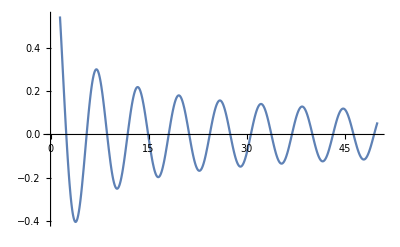

```mathematica
Plot[BesselJ[0,x],{x,0,50}]
```

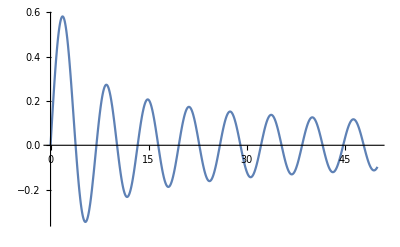

```mathematica
Plot[BesselJ[1,x],{x,0,50}]
```

```mathematica
Asymptotic[ BesselJ[1,x] , x-> ∞ ]
```

(3 Cos[x])/(8 √π x^(3/2))-Cos[x]/(√π √x)+(3 Sin[x])/(8 √π x^(3/2))+Sin[x]/(√π √x)

```mathematica
?BesselK
```

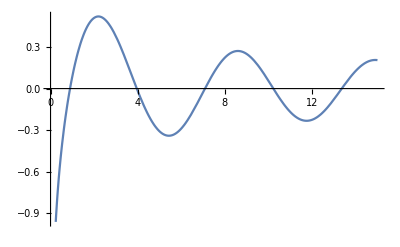

```mathematica
Plot[BesselY[0,r],{r,0,15}]
```

```mathematica
Asymptotic[ BesselY[0,x] , x-> ∞ ]
```

((-1)^(3/4) ⅇ^(-ⅈ x))/(√(2 π) √x)-((-1)^(1/4) ⅇ^(ⅈ x))/(√(2 π) √x)

```mathematica
Asymptotic[ BesselY[1,x] , x-> ∞ ]
```

-((-1)^(1/4) ⅇ^(-ⅈ x))/(√(2 π) √x)+((-1)^(3/4) ⅇ^(ⅈ x))/(√(2 π) √x)

## Construction of Null Tetrad... For Which Metric? Tensors Need To Be Calculated First

```mathematica
(* NULL TETRAD APPENDIX B&7 *)
```

```mathematica
(* PLEASE NOTE:  WE USE THE NEWMAN PENROSE CONVENTION  (l,n,m,mbar) which corresponds to their (k,m,t,tbar) .  My apologies *)
```

```mathematica
Clear[ℓ]
ℓ=
(1/(√2)){1,0,0,1}
```

{1/(√2),0,0,1/(√2)}

```mathematica
Clear[𝓃]
𝓃 = 
(1/(√2)){1,0,0,-1}
```

{1/(√2),0,0,-1/(√2)}

```mathematica
Clear[𝓂]
𝓂 = 
(1/(√2)){0,1,ⅈ,0}
```

{0,1/(√2),ⅈ/(√2),0}

```mathematica
Clear[𝓂bar]
𝓂bar =
(1/(√2)){0,1,0ⅈ,0}
```

{0,1/(√2),0,0}

```mathematica
(* Always check if indices needed are up or down and these are DOWN *) 
l = ToTensor[ {"NewTensor" , "l"} , tensorList[[1]] , ℓ , {0μ}]
n = ToTensor[{"NewTensor" , "n" } , tensorList[[1]] , 𝓃 , {0μ} ] 
m = ToTensor[{"NewTensor" , "m" } , tensorList[[1]] , 𝓂 , {0μ} ] 
mbar = ToTensor[{"NewTensor" , "mbar" } , tensorList[[1]] , 𝓂bar , {0μ} ]
```

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,l},tensorList⟦1⟧,{1/(√2),0,0,1/(√2)},{0}}

$Aborted

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,n},tensorList⟦1⟧,{1/(√2),0,0,-1/(√2)},{0}}

$Aborted

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,m},tensorList⟦1⟧,{0,1/(√2),ⅈ/(√2),0},{0}}

$Aborted

Part::partd: Part specification tensorList⟦1⟧ is longer than depth of object.

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,mbar},tensorList⟦1⟧,{0,1/(√2),0,0},{0}}

$Aborted

```mathematica
TensorValues[ContractIndices[l[-μ]l[μ]]] == 0  // Expand // Simplify 
TensorValues[ContractIndices[n[-μ]n[μ]] ]== 0   // Expand // Simplify 
TensorValues[ContractIndices[m[-μ]m[μ]]] == 0   // Expand // FullSimplify 
TensorValues[ContractIndices[mbar[-μ]mbar[μ]]] == 0  // Expand // FullSimplify 
TensorValues[ContractIndices[l[-μ]n[μ]]] == 1// Expand // FullSimplify 
TensorValues[ContractIndices[l[μ]n[-μ]]] == 1  // Expand // FullSimplify 
TensorValues[ContractIndices[m[-μ]mbar[μ]]] == - 1 // Expand // FullSimplify 
TensorValues[ContractIndices[m[μ]mbar[-μ]]] == - 1 // Expand // FullSimplify 
Clear[completenessDownIndices]
completenessDownIndices = 
MergeTensors[l[-μ]n[-ν]+n[-μ]l[-ν] - m[-μ]mbar[-ν]- m[-ν]mbar[-μ]]  ;
TensorValues[ completenessDownIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[metric2pt22] == 
Flatten[ TensorValues[ completenessDownIndices ]] ] // Expand // FullSimplify  // TableForm

Clear[completenessUpIndices]
completenessUpIndices = 
MergeTensors[l[μ]n[ν]+n[μ]l[ν] - m[μ]mbar[ν]- m[ν]mbar[μ]]  ;
TensorValues[ completenessUpIndices ]   // Expand // FullSimplify // MatrixForm

Thread[Flatten[inverse2pt22] == 
Flatten[ TensorValues[ completenessUpIndices ]] ]  // Expand // FullSimplify  // TableForm
```

Invalid call to TensorValues[]. Unexpected parameters: {l[-μ] l[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {n[-μ] n[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {m[-μ] m[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {mbar[-μ] mbar[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {l[-μ] n[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {l[μ] n[-μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {m[-μ] mbar[μ]}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {m[μ] mbar[-μ]}

$Aborted

Passed Option 'NestQuantity→0' did not satisfy test.
OptionValue of NestQuantity must be a positive Integer.

Aborting in MergeTensors[].

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {completenessDownIndices}

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[metric2pt22].

Invalid call to TensorValues[]. Unexpected parameters: {completenessDownIndices}

$Aborted

Passed Option 'NestQuantity→0' did not satisfy test.
OptionValue of NestQuantity must be a positive Integer.

Aborting in MergeTensors[].

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {completenessUpIndices}

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[inverse2pt22].

Invalid call to TensorValues[]. Unexpected parameters: {completenessUpIndices}

$Aborted